```mathematica
Clear["Global`*"]
```

```mathematica
metaFile = FileNameJoin[{NotebookDirectory[],"output/gpu/meta.dat"}];
TcpuFile = FileNameJoin[{NotebookDirectory[],"output/cpu/T.dat"}];
TgpuFile = FileNameJoin[{NotebookDirectory[],"output/gpu/T.dat"}];
xFile = FileNameJoin[{NotebookDirectory[],"output/gpu/x.dat"}];
```

```mathematica
Lt = BinaryRead[metaFile, "UnsignedInteger32"]
Lx = BinaryRead[metaFile, "UnsignedInteger32"]
Close[metaFile];
```

131072

1024

```mathematica
Tcpu = BinaryReadList[TcpuFile, "Real32"];
Tgpu = BinaryReadList[TgpuFile, "Real32"];
x = BinaryReadList[xFile, "Real32"];
```

```mathematica
Tcpu = ArrayReshape[Tcpu , {Lt, Lx}];
Tgpu = ArrayReshape[Tgpu , {Lt, Lx}];
```

```mathematica
Dimensions[Tgpu]
```

{131072,1024}

```mathematica
Manipulate[ListPlot[Transpose[{x,Tgpu[[n]]}], ImageSize->Large],{n,1,Lt,1}]
```

```mathematica
Manipulate[ListPlot[Transpose[{x,Tcpu[[n]]}], ImageSize->Large],{n,1,Lt,1}]
```

```mathematica
Manipulate[ListPlot[{Transpose[{x,Tcpu[[n]]}],Transpose[{x,Tgpu[[n]]}]}, ImageSize->Large],{n,1,Lt,1}]
```

```mathematica
Manipulate[ListPlot[Transpose[{x,Tgpu[[n]] - Tcpu[[n]]}], ImageSize->Large],{n,1,Lt,1}]
```

```mathematica
Max[Tgpu - Tcpu]
```

Indeterminate

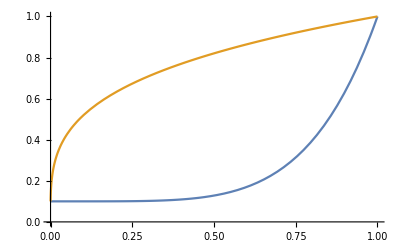

```mathematica
Plot[{0.1 + 0.9 x^5,(0.1^3.5+(1-0.1^3.5)x)^(2/7)},{x,0,1}]
```

```mathematica
Plot[]
```

Plot::argrx: Plot called with 0 arguments; 2 arguments are expected.

Plot[]